```mathematica
(*Problem 2: Computation of expected First Passage Time (FPT) of a LIF neuron. *)
lower = -100; upper = 20; A = 6; B =40;
sol = DSolve[{A T'[x]+1/2 B T''[x] == -1, {T[upper]==0,T[lower]==0}},T[x], x]//Simplify
```

{{T[x]→-(100-120 ⅇ^(6-(3 x)/10)-ⅇ^36 (-20+x)+x)/(6-6 ⅇ^36)}}

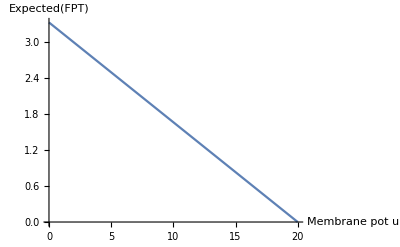

```mathematica
Plot[T[x]/.sol/.{C->20},{x,0,upper},PlotRange->All,AxesLabel->{Membrane pot (u), Expected[FPT]}]
```